## Plotten von Funktionenfolgen und -reihen

Dieses kurze Mathematica Notebook erklärt Grundlegendes zur Darstellung und zum Plotten von Funktionenfolgen und - reihen
												(C) R.S., April 2013

Zu Beginn definieren wir die (Glieder der) Funktionenfolge (siehe Aufgabe 2, Blatt 19).

```mathematica
f[x_,n_]:=(-x)^n
```

So können wir die ersten Glieder der Folge anzeigen lassen.

```mathematica
Table[f[x,n],{n,0,9}]
```

{1,-x,x^2,-x^3,x^4,-x^5,x^6,-x^7,x^8,-x^9}

Der verwendete Befehl Table hat dabei folgende Syntax.

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "}"}]}], "]"}] generates a list of SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from StyleBox["1", "TR"] to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], StyleBox["…", "TR"].
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

Die Ausageb erfolgt in einer Liste. Diese können wir zum Zeichnen der Grapen an den Plot - Befehl übergeben.

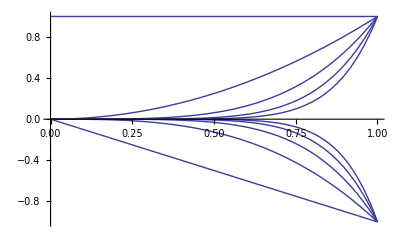

```mathematica
Plot[Table[f[x,n],{n,0,9}],{x,0,1}]
```

Die Syntax des Plot - Befehls ist dabei :

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Zur Darstellung der Partialsummen der zugeordneten Funktionenreihe verwenden wir :

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1,i_2,….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

```mathematica
Sum[f[x,k],{k,0,9}]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9

Um eine Liste der ersten Partilasummen zu erhalten kombinieren wir Sum und Table.

```mathematica
Table[Sum[f[x,k],{k,0,n}],{n,0,9}]
```

{1,1-x,1-x+x^2,1-x+x^2-x^3,1-x+x^2-x^3+x^4,1-x+x^2-x^3+x^4-x^5,1-x+x^2-x^3+x^4-x^5+x^6,1-x+x^2-x^3+x^4-x^5+x^6-x^7,1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8,1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9}

Zum Zeichnen der Graphen der ersten Partialsummen kombinieren wir weiters mit dem Plot - Befehl

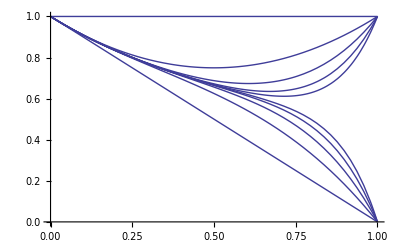

```mathematica
Plot[Table[Sum[f[x,k],{k,0,n}],{n,0,9}],{x,0,1}]
```

Plotten wir mehr Partialsummen, so können mehr über das Konvergenzverhalten antizipieren.  Allerdings verlängerts sich die Wartezeit...

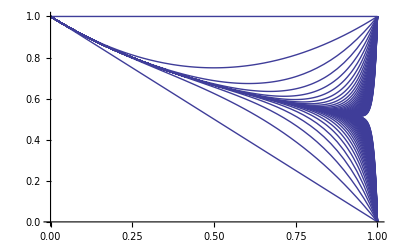

```mathematica
Plot[Table[Sum[f[x,k],{k,0,n}],{n,0,100}],{x,0,1}]
```

Um den Grenzwert ebenfalls zu zeichnen, können wir den Grafik - Befehl Show verwenden. Dieser eröffnet in Kombination mit Graphics vielfältige Möglichkeiten.

```mathematica
?Graphics
?Show
```

Graphics[primitives,options] represents a two-dimensional graphical image.

RowBox[{"Show", "[", RowBox[{StyleBox["graphics", "TI"], ",", StyleBox["options", "TI"]}], "]"}] shows graphics with the specified options added. 
RowBox[{"Show", "[", RowBox[{SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] shows several graphics combined.

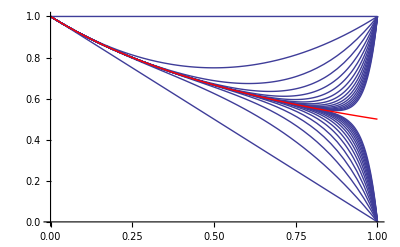

```mathematica
a:=Plot[Table[Sum[f[x,k],{k,0,n}],{n,0,30}],{x,0,1}]
b:=Plot[1/(1+x),{x,0,1},PlotStyle->{Red,Thick}]
Show[a,b]
```

Natürlich kann Mathematica den Grenzwert der Reihe ausrechnen-- - das gibt aber keinen Beweis und über Bereich und Art der Konvergenz erfärt man so nichts ...

```mathematica
Sum[f[x,n],{n,0,Infinity}]
```

1/(1+x)